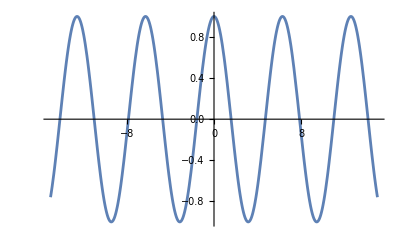

```mathematica
Plot[Cos[x],{x,-15,15}]
```

```mathematica
d={δ,f,x}↦(f[x+δ]-f[x])/(Identity[x+δ]-x)
```

Function[{δ,f,x},(f[x+δ]-f[x])/(Identity[x+δ]-x)]

```mathematica
Manipulate[Plot[{
d[δ,Sin,x],
Cos[x]
},{x,-15,15}],
{δ,0.01,10}
]
```

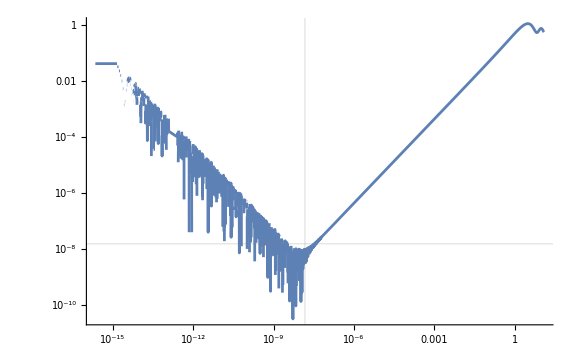

```mathematica
LogLogPlot[Abs[d[δ,Sin,1]-Cos[1]],{δ,$MachineEpsilon,4π},GridLines->{{√($MachineEpsilon)},{√($MachineEpsilon)}}]
```

```mathematica
d2={δ,f,x}↦(f[x+δ]-f[x-δ])/(2(Identity[x+δ]-x));
```

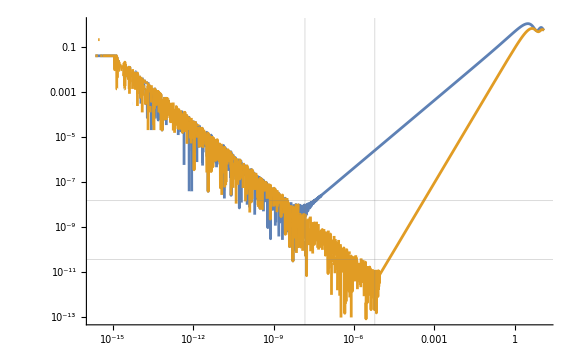

```mathematica
LogLogPlot[
{Abs[d[δ,Sin,1]-Cos[1]],Abs[d2[δ,Sin,1]-Cos[1]]},
{δ,$MachineEpsilon,4π},
GridLines->{{√($MachineEpsilon),($MachineEpsilon)^(1/3)},{√($MachineEpsilon),($MachineEpsilon)^(2/3)}}
]
```